```mathematica
(***********************************************
Code corresponing to the publication
"New insights into mRNA trafficking in axons"
LF Gumy,EA Katrukha,LC Kapitein,CC Hoogenraad-Developmental neurobiology,2014

Part 1: average probability density function (PDF) approach

email katpyxa@gmail.com for any questions
GNU General Public License
********************)

(*MAIN PARAMETERS*)
(*diffusion coefficient in um^2/s*)
dDcoeff = 0.495;
(*velocity in um/s*)
dVelocity=0.1;
(*length of axon in um*)
dLength = 300;
(*end time of solution calculation in seconds *)
Tfinal = 43200.;
Tfinal = 4200.;
(*axon length is splitted to this number of intervals*)
n = 1000;
Subscript[h, n] = 1/n*dLength;
(*parameters of initial distribution at t=0*)
(*position of center xc*)
Subscript[x, c]=7;
(*width*)
σ=4;

(*defining equations in finite differences*)
U[t_] = Table[Subscript[u, i][t],{i,0,n}];
deriv=ListCorrelate[{(dDcoeff/Subscript[h, n]^2)+(dVelocity/Subscript[h, n]),-(dVelocity/Subscript[h, n])-2*(dDcoeff/Subscript[h, n]^2),(dDcoeff/Subscript[h, n]^2)}, U[t],{1,2}];
derivv = Table[deriv[[i]],{i,1,n-1}];
eqns = Thread[D[U[t],t] == Join[{(dDcoeff/Subscript[h, n]^2)*(-Subscript[u, 0][t]+Subscript[u, 1][t])-(dVelocity/Subscript[h, n])*Subscript[u, 0][t]},derivv,{(dVelocity/Subscript[h, n])*Subscript[u, n-1][t]+dDcoeff*(Subscript[u, n-1][t]-Subscript[u, n][t])/Subscript[h, n]^2}]];

(*Initial distribution*)
kk=Table[0.26*Exp[-(i*Subscript[h, n]-Subscript[x, c])^2/(2*σ*σ)],{i,0,n}];

initc = Thread[U[0] == kk];
(* now let's solve everything! *)
Print["Please wait, solving equations..."];
lines = NDSolve[{eqns, initc},U[t],{t,0,Tfinal}];
(*it may take some time*)
Print["Done."];
```

```mathematica
(* make animated version *)
nTimeFrames=120;
MovieAnimat={}; 
For[dt=0,dt<=Tfinal,dt+=Tfinal/nTimeFrames,
MovieAnimat = Join[MovieAnimat,{ListPlot[Table[{i Subscript[h, n],First[Subscript[u, i][t] /.lines]/.t->dt},{i,0,n}], Joined->True, PlotLabel->DateString[DateList[dt],{"Time: ","Hour","h ","Minute","min"}],PlotStyle->Thick,PlotRange->{{0,dLength},{0,Max[kk]}}]}];
];
ListAnimate[MovieAnimat,AnimationRunning->False]
```

```mathematica
(*export movie*)
SetDirectory["C:\\Users\\Eugene\\Desktop"];
(**SetDirectory["/home/eugene"];**)
Export["diffusion.avi",MovieAnimat,"FrameRate"->10]
```

diffusion.gif

```mathematica
(*3D version*)
nTimeFrames=50;
Table3D={};
For[i=0,i≤n,i+=2,
For[dt=0,dt<=Tfinal,dt+=Tfinal/nTimeFrames,
Table3D = Join[Table3D,{{i Subscript[h, n],dt,First[Subscript[u, i][t] /.lines]/.t->dt}}];
];
];
ListPlot3D[Table3D, PlotRange->{{0,dLength},{0,Tfinal},{0,Max[kk]}}]
```

-Graphics3D-

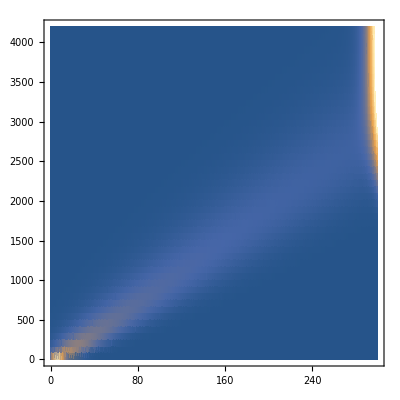

```mathematica
(*or density plot*)
ListDensityPlot[Table3D, PlotRange->{{0,dLength},{0,Tfinal},{0,Max[kk]}}]
```

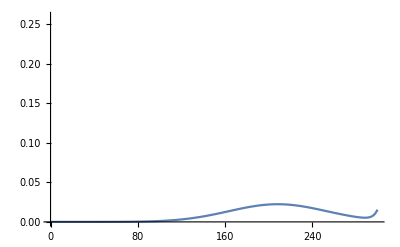

```mathematica
(*show PDF for specific time point*)
tx=2000;
ListPlot[Table[{i Subscript[h, n],First[Subscript[u, i][t] /.lines]/.t->tx},{i,0,n}], Joined->True, PlotRange->{{0,dLength},{0,Max[kk]}}]
```

```mathematica
(* export PDF plot for specific time point *)
tx=2000;
type="20130715_P=0.6_v=0.1+D=0.495_";
path = "F:\\papers\\mRNA_review\\";
filename = StringJoin[path,type,"_43200s.dat"];
Export[filename,N[Table[{i Subscript[h, n],First[Subscript[u, i][t] /.lines]/.t->tx},{i,0,n}]]]
```